```mathematica
spfan=Import["G:\\calc-online\\gpd\\pic\\pic3Dlist-a-n-xi3.wdx"];
f2n=Flatten[Query[2,1]@spfan,1];
g2n=Flatten[Query[2,2]@spfan,1];
f1n=Flatten[Query[1,1]@spfan,1];
g1n=Flatten[Query[1,2]@spfan,1];
```

```mathematica
(*注意计算得到的list两个变量是(y,t)*)
```

```mathematica
lf2n=Interpolation[f2n];
sf2[x_]=lf2n[x,-1];
lf1n=Interpolation[f1n];
sf1[x_]=lf1n[x,-1];
```

```mathematica
NIntegrate[sf2[x],{x,0.3,1}]
```

1.11907

```mathematica
NIntegrate[sf1[x],{x,-0.3,0.3}]
```

-0.882834

```mathematica
(*ERBL-gda part*)
Fp[s_]=1/(1-s/λ1^2);
Φ[z_,η_,s_]=6*z*(1-z)*(2η-1)*Fp[s];
ph[t_]=Φ[(x/0.3+1)/2,(y/0.3+1)/2,t]/.{λ1->0.79};
inf1[x_]=(sf1[y]/(2y))*ph[-1];
InAf1[x_]:=NIntegrate[inf1[x],{y,-0.3,0.3},AccuracyGoal->10];
```

```mathematica
Simplify[inf1[0.1]/.{y->0.1}]
```

-0.535003

```mathematica
InAf1[0.1]
```

-0.75389

```mathematica
Parallelize[pfea=Table[{x,InAf1[x]},{x,-0.3,0.3,0.01}]];
```

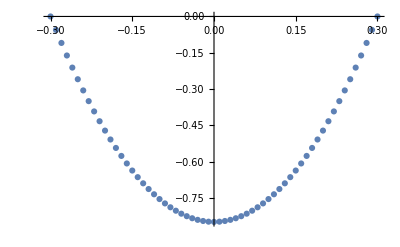

```mathematica
ListPlot[pfea]
```

```mathematica
NIntegrate[inf1[0.3],{y,-0.3,0.3},AccuracyGoal->10]
```

0.

```mathematica
(*ERBL-gpd part*)
```

```mathematica
Hqz1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*(1/2*2.6*β^(0.75-1)(1-β)^0.95)/(1-t/λ1^2);
Hqf1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*(-1/2*2.6*Abs[β]^(0.75-1)(1-Abs[β])^0.95)/(1-t/λ1^2);
Hqf2=(Hqf1/.{α->(x-β)/ξ})/ξ;
Hqz2=(Hqz1/.{α->(x-β)/ξ})/ξ;
Hqfn2[x_]=Hqf2/.{b0->2,ξ->0.3/y,x->x/y,λ1->0.79,t->-1};
Hqzn2[x_]=Hqz2/.{b0->2,ξ->0.3/y,x->x/y,λ1->0.79,t->-1};
```

```mathematica
Hf2qf[x_]=Hqfn2[x]*sf2[y]/y;
Hf2qz[x_]=Hqzn2[x]*sf2[y]/y;
```

```mathematica
(*注意这里sf2是已经完成了k和θ积分的*)
```

```mathematica
inf[x_]:=NIntegrate[Hf2qf[x],{y,0.3,1},{β,(x-0.3)/(y+0.3),0}];
inz[x_]:=NIntegrate[Hf2qz[x],{y,0.3,1},{β,0,(x+0.3)/(y+0.3)}];
```

```mathematica
inf[-0.1]
```

-1.13291

```mathematica
inz[0.1]
```

1.13291

```mathematica
InHf2q[x_]:=NIntegrate[Hf2qf[x],{y,0.3,1},{β,(x-0.3)/(y+0.3),0}]+NIntegrate[Hf2qz[x],{y,0.3,1},{β,0,(x+0.3)/(y+0.3)}];
```

```mathematica
InHf2q[0.3]
```

0.584814

```mathematica
Table[{x,InHf2q[x]},{x,-0.3,0.3,0.01}];
```

```mathematica
pf=%25;
```

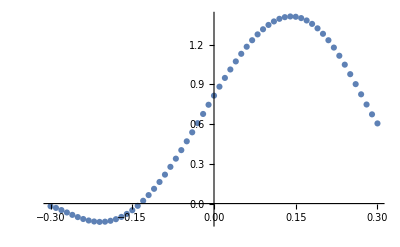

```mathematica
ListPlot[pf]
```

```mathematica
(*DGLAPpart*)
Hq1=(Gamma[2*b0+2]*((1-Abs[β])^2-α^2)^b0/(2^(2*b0+1)*(Gamma[b0+1])^2*(1-Abs[β])^(2b0+1)))*Nv*β^(a-1)*(1-β)^b1*(1+c*β^d)/(1-t/λ1^2);
Hqa=(Hq1/.{α->(x-β)/ξ})/ξ;
Hqan=Hqa/.{a->0.7,b1->2,c->13.8,d->2,Nv->1/2,b0->2,λ1->0.79,t->-1,ξ->0.3,x->0.5};
Hqay[x_]=Hqa/.{a->0.7,b1->2,c->13.8,d->2,Nv->1/2,b0->2,λ1->0.79,t->-1,ξ->0.3/y,x->x/y};
Hf2q[x_]=Hqay[x]*sf2[y]/y;
InHf2qD[x_]:=NIntegrate[Hf2q[x],{y,x,1},{β,(x-0.3)/(y-0.3),(x+0.3)/(y+0.3)}];
```

```mathematica
InHf2qD[0.5]
```

0.0399664

```mathematica
Parallelize[pfd=Table[{x,InHf2qD[x]},{x,0.3,1,0.01}]];
```

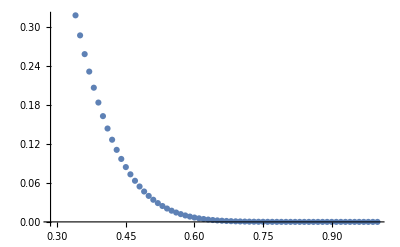

```mathematica
ListPlot[pfd]
```

```mathematica
(*真正的3d图*)
```

```mathematica
Ef3df[x_,t_]=Hqfn2[x]*lf2n[y,t]/y;
Ef3dz[x_,t_]=Hqzn2[x]*lf2n[y,t]/y;
Df3d[x_,t_]=Hqay[x]*lf2n[y,t]/y;
Eaf3d[x_,t_]=(lf1n[y,t]/(2y))*ph[t];
```

```mathematica
NIntegrate[Df3d[0.5,-1],{y,0.5,1},{β,(0.5-0.3)/(y-0.3),(0.5+0.3)/(y+0.3)}]
```

0.0399664

```mathematica
NIntegrate[Eaf3d[0.1,-1],{y,-0.3,0.3}]
```

-0.75389

```mathematica
Dinf3d[x_,t_]:=NIntegrate[Df3d[x,t],{y,x,1},{β,(x-0.3)/(y-0.3),(x+0.3)/(y+0.3)}];
Einf3d[x_,t_]:=NIntegrate[Ef3df[x,t],{y,0.3,1},{β,(x-0.3)/(y+0.3),0}]+NIntegrate[Ef3dz[x,t],{y,0.3,1},{β,0,(x+0.3)/(y+0.3)}];
Eainf3d[x_,t_]:=NIntegrate[Eaf3d[x,t],{y,-0.3,0.3},AccuracyGoal->10];
```

```mathematica
Einf3d[0.1,-1]
```

1.34828

```mathematica
Dinf3d[0.5,-1]
```

0.0399664

```mathematica
Eainf3d[0.1,-1]
```

-0.75389

```mathematica
Parallelize[lfD3d=Table[{{x,t},Dinf3d[x,t]},{x,0.3,1,0.005},{t,-1,-0.3488127032967032,0.01}]];(*about 2 hours*)
```

```mathematica
tsetfD=Interpolation[Flatten[lfD3d,1]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[tsetfD[x,y],{x,0.3,1.},{y,-1.,-0.35},PlotRange->All]
```

-Graphics3D-

```mathematica
lfD3d=ParallelTable[{{x,t},Dinf3d[x,t]},{x,0.3,1,0.005},{t,-1,-0.3488127032967032,0.01}];
lfEG3d=ParallelTable[{{x,t},Einf3d[x,t]},{x,-0.3,0.3,0.005},{t,-1,-0.3488127032967032,0.01}];
lfEA3d=ParallelTable[{{x,t},Eainf3d[x,t]},{x,-0.3,0.3,0.005},{t,-1,-0.3488127032967032,0.01}];
```

```mathematica
tfD=Interpolation[Flatten[lfD3d,1]];
tfEG=Interpolation[Flatten[lfEG3d,1]];
tfEA=Interpolation[Flatten[lfEA3d,1]];
```

```mathematica
path=FileNameJoin[{"G:\\calc-online\\gpd\\pic",
"33test.wdx"}];
```

```mathematica
test=<|"1"->tfD,"2"->tfEG,"2"->tfEA|>;
```

```mathematica
Export[path,test]
```

G:\calc-online\gpd\pic\33test.wdx

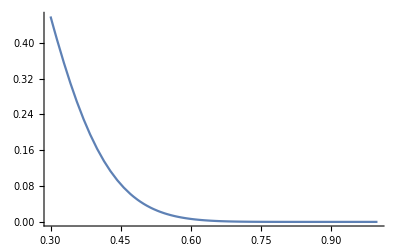

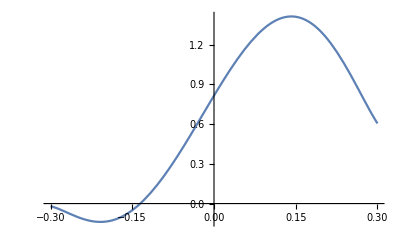

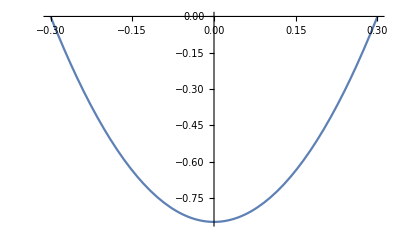

```mathematica
Plot[tfD[x,-1],{x,0.3,1},PlotRange->All]
Plot[tfEG[x,-1],{x,-0.3,0.3}]
Plot[tfEA[x,-1],{x,-0.3,0.3}]
```

```mathematica
cob[x]=Piecewise[{{tfD[x,-1],x>0.3},{tfEA[x,-1]+tfEG[x,-1],x<0.3}},{x,-0.3,1}];
```

Set::write: Tag If in If[x>0.3,tfD,tfEA+tfEG][x] is Protected.

```mathematica
tes[x_]=Piecewise[{{tfD[x,-1],x>0.3},{tfEA[x,-1]+tfEG[x,-1],x<0.3}},{x,-0.3,1}]
```

Piecewise[{{InterpolatingFunction[…][x,-1], x>0.3}, {InterpolatingFunction[…][x,-1]+InterpolatingFunction[…][x,-1], x<0.3}, {{x,-0.3,1}, True}}]

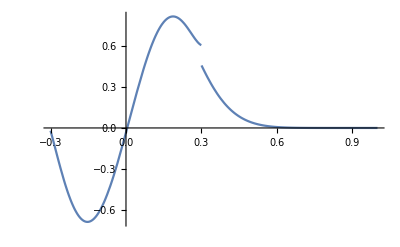

```mathematica
Plot[tes[x],{x,-0.3,1}]
```

```mathematica
tfEG[0.3,-1]
```

0.60494

```mathematica
tfD[0.3,-1]
```

0.458463

```mathematica
t2[x_,t_]=Piecewise[{{tfD[x,t],x>0.3},{tfEA[x,t]+tfEG[x,t],x<0.3}},{x,-0.3,1}]
```

Piecewise[{{InterpolatingFunction[…][x,t], x>0.3}, {InterpolatingFunction[…][x,t]+InterpolatingFunction[…][x,t], x<0.3}, {{x,-0.3,1}, True}}]

```mathematica
Plot3D[t2[x,t],{x,-0.3,1},{t,-1,-0.35},AxesLabel->Automatic]
```

-Graphics3D-